```mathematica
θ[x_,y_] := ArcTan[x,y]
r[x_,y_]:= √(x^2+y^2)
```

```mathematica
f[θ_,c_]:= 2 Sin[θ]^2/(1 + c - Cos[θ])
v[r_,θ_,c_]:= (-f[θ,c])/(r Sin[θ])
u[r_,θ_,c_]:= 1/(r Sin[θ])((4 Cos[θ] Sin[θ])/(1+c-Cos[θ])-(2 Sin[θ]^3)/(1+c-Cos[θ])^2)
```

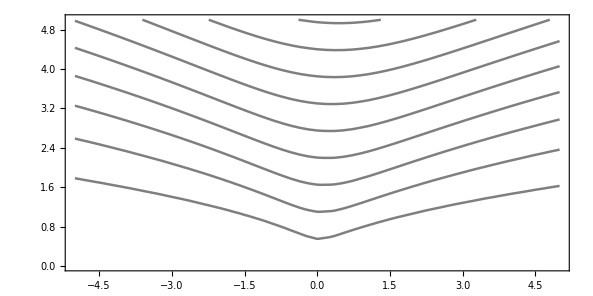

```mathematica
Jet=ContourPlot[r[x,y] f[θ[x,y],10],{x,-5,5},{y,0,5},AspectRatio -> 1/2,ContourShading -> False,ContourLabels-> Automatic,Contours -> {1/10,2/10,3/10,4/10,5/10,6/10,7/10,8/10,9/10,10/10,11/10},ContourStyle -> Thickness[0.003]]
```

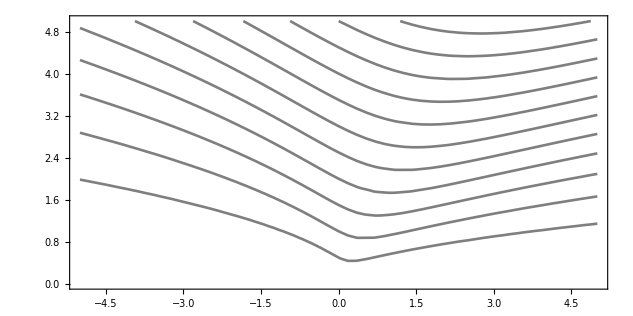

```mathematica
Jet=ContourPlot[r[x,y] f[θ[x,y],1],{x,-5,5},{y,0,5},AspectRatio -> 1/2,ContourShading -> False,ContourLabels-> Automatic,Contours -> {1/2,2/2,3/2,4/2,5/2,6/2,7/2,8/2,9/2,10/2,11/2},ContourStyle -> Thickness[0.003]]
```

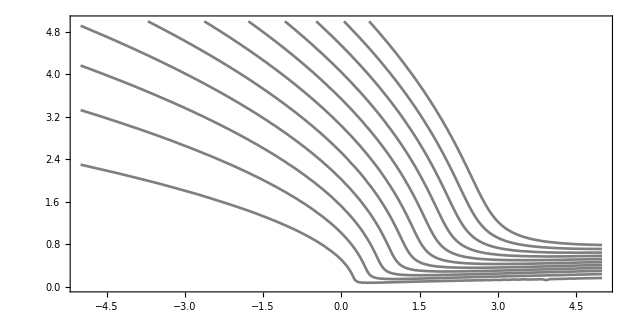

```mathematica
Jet=ContourPlot[r[x,y] f[θ[x,y],0.01],{x,-5,5},{y,0,5},AspectRatio -> 1/2,ContourShading -> False,ContourLabels-> Automatic,Contours -> {1,2,3,4,5,6,7,8,9,10,11},ContourStyle -> Thickness[0.003]]
```

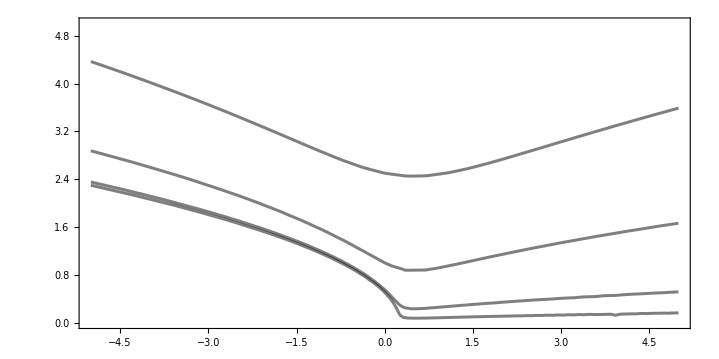

```mathematica
p1 = ContourPlot[r[x,y] f[θ[x,y],.01],{x,-5,5},{y,0,5},AspectRatio -> 1/2,ContourShading -> False,Contours -> {1},ContourStyle -> Thickness[0.003]];
p2 = ContourPlot[r[x,y] f[θ[x,y],.1],{x,-5,5},{y,0,5},AspectRatio -> 1/2,ContourShading -> False,Contours -> {1},ContourStyle -> Thickness[0.003]];
p3 = ContourPlot[r[x,y] f[θ[x,y],1],{x,-5,5},{y,0,5},AspectRatio -> 1/2,ContourShading -> False,Contours -> {1},ContourStyle -> Thickness[0.003]];
p4 = ContourPlot[r[x,y] f[θ[x,y],4],{x,-5,5},{y,0,5},AspectRatio -> 1/2,ContourShading -> False,Contours -> {1},ContourStyle -> Thickness[0.003]];
Show[p1,p2,p3,p4]
```

```mathematica
θo[c_] := ArcCos[1/(1 + c)]
```

```mathematica
Spread = Plot[x Sin[θo[0.01]],{x,0,5},PlotStyle -> Thickness[0.005]];
```

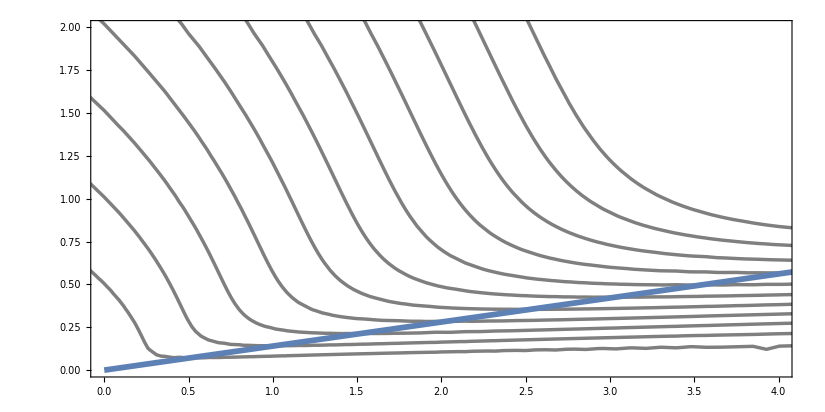

```mathematica
Show[Jet,Spread,PlotRange -> {{0,4},{0,2}}]
```

```mathematica
ω[r_,θ_,c_]:= √((1/rr D[rr v[rr,tt,cc],rr] - 1/rr D[u[rr,tt,cc],tt])^2) /. {rr -> r,tt -> θ,cc -> c}
```

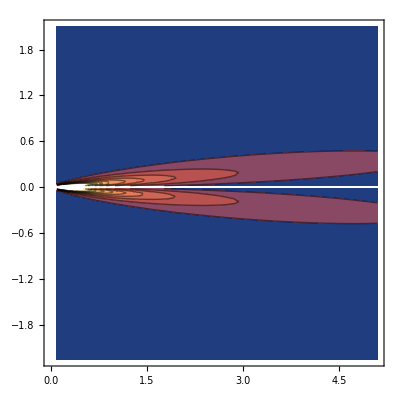

```mathematica
ContourPlot[ω[r[x,y],θ[x,y],.01],{x,0.1,5.1},{y,-2.25,2.1},PlotRange -> {0,5000}]
```

```mathematica
Manipulate[ContourPlot[r[x,y] f[θ[x,y],c],{x,-5,5},{y,0,5},AspectRatio -> 1/2,ContourShading -> False,ContourLabels-> Automatic,Contours -> Table[l,{l,-δl,20,δl}],ContourStyle -> Thickness[0.003],PlotPoints -> 100,PlotLabel->4/c],
{c,0.02,10},{δl,.1,1}]
```